## Study the evolution of the minimum values of H with angular momentum

```mathematica
TSD2={1739.9,1936.5,2199.6,2514.5,2900.8,3351.1,3866.4,4445.0,5084.0,5781.0,6533.6,7339.1,8196.9,9106.6,10069.2,11085.7,12156.8,13283.0,14462.3,15689,16958,18262};
SPIN2=Table[6.5+2i,{i,0,21}];
DATA2=Table[{SPIN2[[i]],TSD2[[i]]},{i,1,Length[TSD2]}];
```

## Expression & Parameters

```mathematica
IF[X_]:=1/(2*X);
I1=72;I2=15;I3=7;V=2.1;γ=22;j=13/2;
m1={π/2,0};m2={π/2,π};m3={π/2,2π};
Hen[I_,θ_,φ_,A1_,A2_,A3_,V_,γ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ]^2(A1*Cos[φ]^2+A2*Sin[φ]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ]-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
```

## The contour plot evolution with spin I

```mathematica
CPH[spin_,I1_,I2_,I3_,V_,γ_,i_]:=Show[ContourPlot[H[spin,θ,φ,IF[I1],IF[I2],IF[I3],V,γ*π/180]/.{j->13/2},{θ,0,π},{φ,-0.1,2.02π},AspectRatio->Automatic,Contours->15,ContourStyle->{{Black,Thickness[0.005],Opacity[1]},{Black,Thick,Thickness[0.006],Opacity[1]}},ImageSize->Scaled[0.52],Frame->True,Axes->False,FrameStyle->Directive[Thick,Black],FrameLabel->{"θ [rad]","φ [rad]"},PlotLabel->Text[Style[StringTemplate["ℐ_1:ℐ_2:ℐ_3=``:``:`` [ℏ^2MeV^-1]\n                 I=`` [ℏ]"][I1,I2,I3,i],Black,Bold,FontFamily->"Times New Roman",15]],PlotLegends->Automatic,LabelStyle->{Black,15,FontFamily->"Times New Roman"}]];
```

## H value within the minimum points evaluation

```mathematica
henValue[I_,p_]:=Hen[I,p[[1]],p[[2]],IF[I1],IF[I2],IF[I3],V,γ];
```

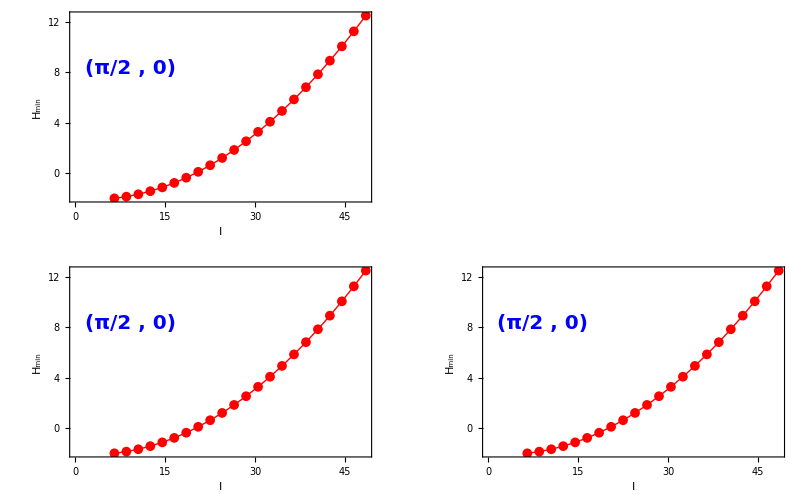

```mathematica
GraphicsGrid[{{ListPlot[Table[{SPIN2[[i]],henValue[SPIN2[[i]],m1]},{i,1,Length[SPIN2]}],Frame->True,Axes->False,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{Thick,Red},FrameStyle->Directive[Black,Thick],FrameLabel->{"I","H_min"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Style["(π/2 , 0)",20,Blue,Bold],Scaled[{0.2,0.7}]]]},{ListPlot[Table[{SPIN2[[i]],henValue[SPIN2[[i]],m2]},{i,1,Length[SPIN2]}],Frame->True,Axes->False,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{Thick,Red},FrameStyle->Directive[Black,Thick],FrameLabel->{"I","H_min"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Style["(π/2 , 0)",20,Blue,Bold],Scaled[{0.2,0.7}]]],ListPlot[Table[{SPIN2[[i]],henValue[SPIN2[[i]],m3]},{i,1,Length[SPIN2]}],Frame->True,Axes->False,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{Thick,Red},FrameStyle->Directive[Black,Thick],FrameLabel->{"I","H_min"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Style["(π/2 , 0)",20,Blue,Bold],Scaled[{0.2,0.7}]]]}},Frame->All,ImageSize->Scaled[1]]
```

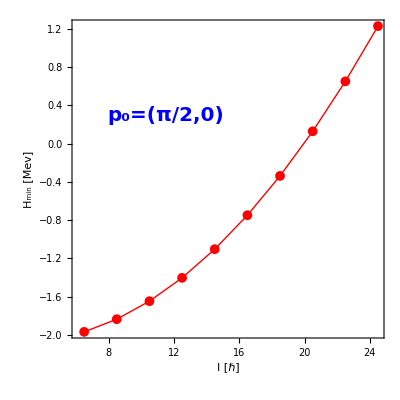

```mathematica
ListPlot[Table[{SPIN2[[i]],henValue[SPIN2[[i]],m1]},{i,1,10}],Frame->True,Axes->True,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{Thick,Red},FrameStyle->Directive[Black,Thick],FrameLabel->{"I [ℏ]","H_min [Mev]"},LabelStyle->{21,Bold,Black,FontFamily->"Times New Roman"},Epilog->Inset[Style["p_0=(π/2,0)",20,Blue,Bold],Scaled[{0.3,0.7}]],PlotRange->Full,AspectRatio->1]
```

```mathematica
(*Epilog->Inset[Style["(π/2 , 0) ; (π/2 , π)\n(π/2 , 2π)",20,Blue,Bold],Scaled[{0.3,0.6}]]*)
```

```mathematica
(□/□
```